{0.1880336115708795609315551561953,0.1315968811280182898995570113772,0.091771243880853153103578564147,0.0637703521715097778660461605902,0.044155234974430996222411711857,0.030464653693795094071111492047,0.02094398222163763453146847817,0.0143471959665378191220305061,0.0097928665729995460780757818,0.0066598720288227923112229002,0.0045121826182287371998385439,0.003044837975775376394333411,0.00204529837875454213928091,0.00136589740554235840861002,0.00090426942182679117512445,0.00058947103626613108176443,0.0003721345287891882852433,0.000217438762924299347726,0.000100000000004502545065,6.796697532×10^-15}

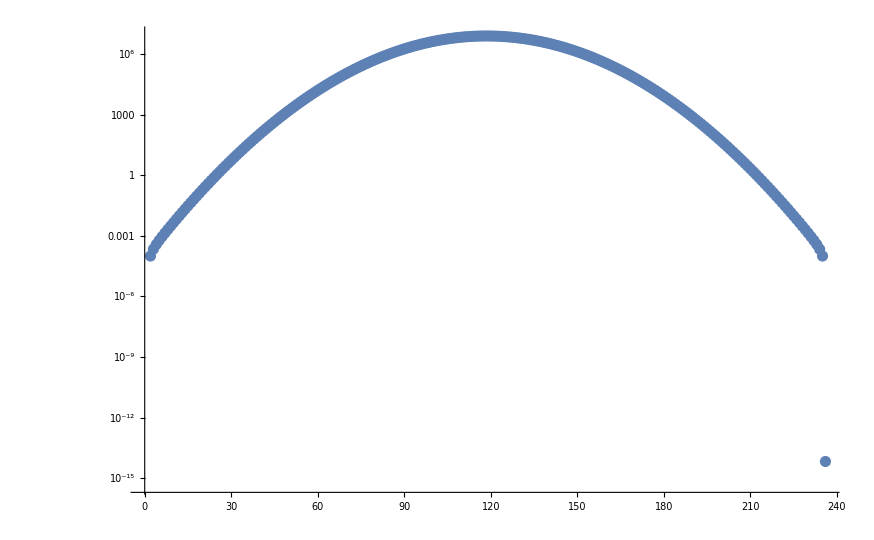

```mathematica
mass=2;
V[r_]=(r-15)^2;
xmin=10;
xmax=20;
nOfPoints=236;
stepSize=(xmax-xmin)/(nOfPoints-1);
energy=0.4998868009845387437379292574102`110;
Q[r_]=2mass*(energy-V[r]);
ψ=Table[0,{nOfPoints}];
ψ[[1]]=0;
ψ[[2]]=10^-4;
Do[ψ[[j+1]]=ψ[[j]](2-stepSize^2*Q[xmin +stepSize(j-1)])-ψ[[j-1]],{j,2,nOfPoints-1}];
(* integral=(Sum[ψ[[j]]^2,{j,2,nOfPoints-1}]+ψ[[nOfPoints]]^2/2)stepSize
ψ=ψ/√integral;*)
Take[ψ,-20]
ListLogPlot[ψ]
```

```mathematica
f=Interpolation[Table[{xmin +stepSize(j-1),ψ[[j]]},{j,1,nOfPoints}],InterpolationOrder->3,Method->"Spline"];
```

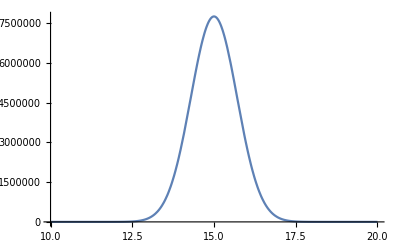

```mathematica
Plot[f[x],{x,10,20},PlotRange->All]
```

{0.0000346720314734064970094209578,0.000021529714190849010039164811,0.000013312080523104057841060462,8.196024129940039971826289×10^-6,5.02471072938468332990919×10^-6,3.06739953581477224450457×10^-6,1.8645838229976984689802×10^-6,1.128616498130016330758×10^-6,6.802426638570907519717×10^-7,4.08256214737069872654×10^-7,2.4397602866717909567×10^-7,1.4517370386623221328×10^-7,8.600012049931210085×10^-8,5.07009836545956977×10^-8,2.97138553797258022×10^-8,1.7254433408944168×10^-8,9.8288938469683739×10^-9,5.317942823283491×10^-9,2.40960459177886×10^-9,2.3914697243297×10^-10}

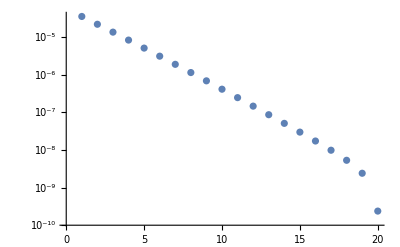

```mathematica
mass=2;
V[r_]=(r-15)^2;
xmin=10;
xmax=21;
nOfPoints=236;
stepSize=(xmax-xmin)/(nOfPoints-1);
energy=0.4998630226723729820676963330252`110;
Q[r_]=2mass*(energy-V[r]);
ψ=Table[0,{nOfPoints}];
ψ[[1]]=0;
ψ[[2]]=10^-4;
Do[ψ[[j+1]]=ψ[[j]](2-stepSize^2*Q[xmin +stepSize(j-1)])-ψ[[j-1]],{j,2,nOfPoints-1}];
(* integral=(Sum[ψ[[j]]^2,{j,2,nOfPoints-1}]+ψ[[nOfPoints]]^2/2)stepSize
ψ=ψ/√integral;*)
Take[ψ,-20]
ListLogPlot[%,PlotRange->Automatic]
```

{1.28229033211240735703×10^-9,6.97068491394336110408×10^-10,3.7705078179538654119×10^-10,2.029369631526629643×10^-10,1.08682846862865245×10^-10,5.79163281355033532×10^-11,3.0710213385537159×10^-11,1.62034719405026×10^-11,8.507037845735873×10^-12,4.44421591034624×10^-12,2.3102520444851×10^-12,1.195005440935×10^-12,6.150604164456×10^-13,3.14966348188×10^-13,1.6041833486×10^-13,8.114783718×10^-14,4.054178207×10^-14,1.9547213×10^-14,8.1514119×10^-15,8.185221×10^-16}

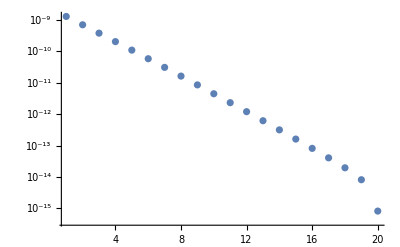

```mathematica
mass=2;
V[r_]=(r-15)^2;
xmin=10;
xmax=22;
nOfPoints=236;
stepSize=(xmax-xmin)/(nOfPoints-1);
energy=0.499836977160225031843288085255757920405689`110;
Q[r_]=2mass*(energy-V[r]);
ψ=Table[0,{nOfPoints}];
ψ[[1]]=0;
ψ[[2]]=10^-4;
Do[ψ[[j+1]]=ψ[[j]](2-stepSize^2*Q[xmin +stepSize(j-1)])-ψ[[j-1]],{j,2,nOfPoints-1}];
(* integral=(Sum[ψ[[j]]^2,{j,2,nOfPoints-1}]+ψ[[nOfPoints]]^2/2)stepSize
ψ=ψ/√integral;*)
Take[ψ,-20]
ListLogPlot[Abs[%],PlotRange->All]
```

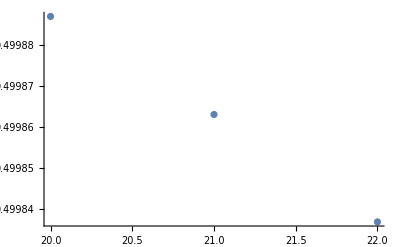

```mathematica
ListPlot[{{20,0.4998868009845387437379292574102`110},{21,0.4998630226723729820676963330252`110},{22,0.499836977160225031843288085255757920405689`110}}]
```